## Объявление глобальных переменных

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.001;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

ErrorBarFunction::shdw: Symbol ErrorBarFunction appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

ErrorBar::shdw: Symbol ErrorBar appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

ErrorListPlot::shdw: Symbol ErrorListPlot appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

## Построение одного графика

### Импорт табличных данных

```mathematica
dataBg=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/55/tables/bg.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataBg//TableForm
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,250}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

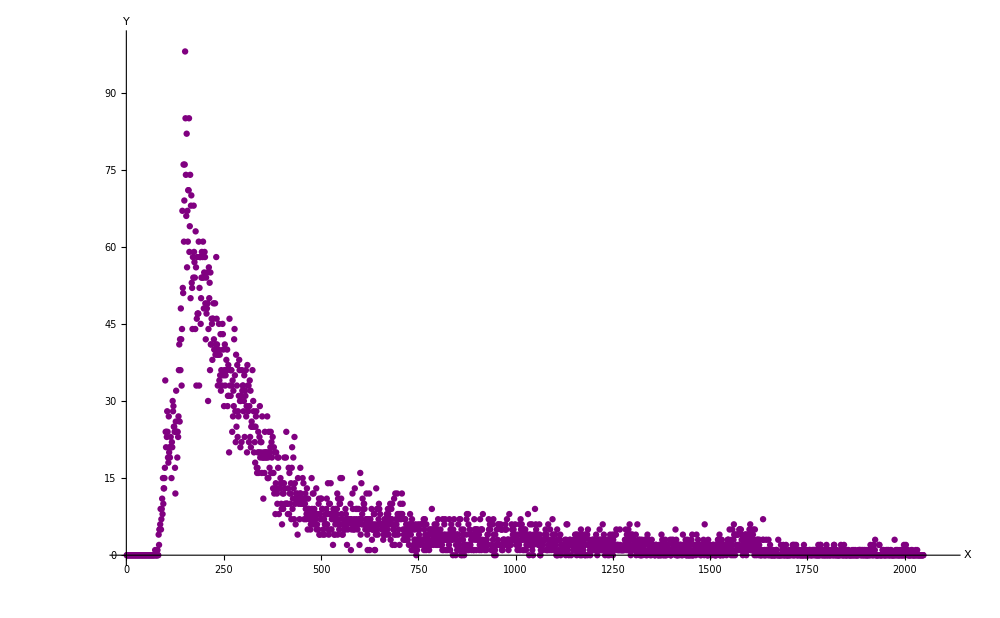

```mathematica
Show[ListPlot[dataBg⟦2;;,{1,2}⟧,
GridLines->{grids@100,grids@5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.003 ,Purple},
Ticks->{myTicX, Automatic}, 
PlotRange->{{0,2100},{0,100}}]]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

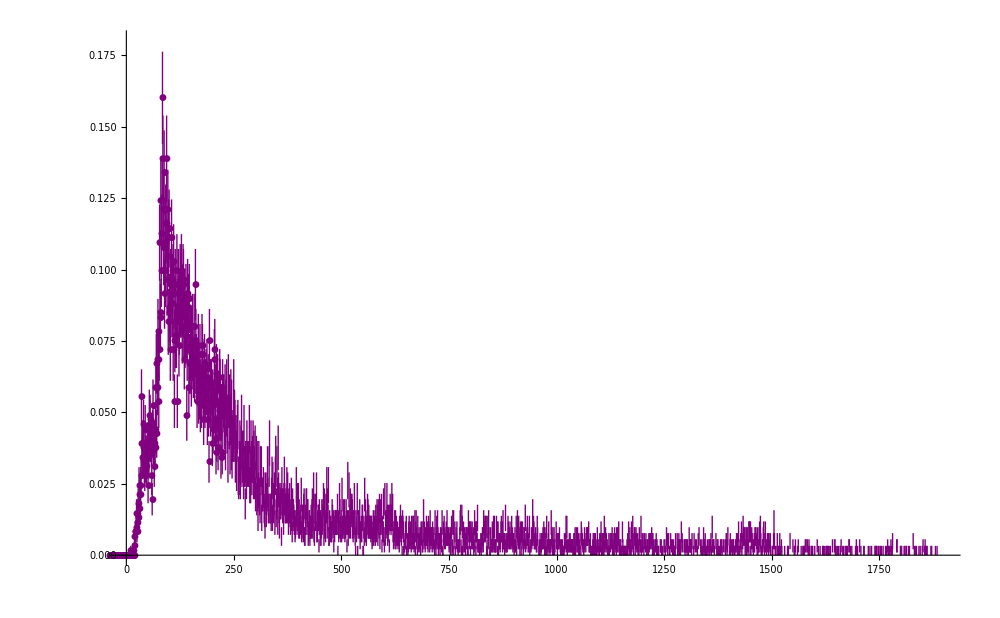

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataBg⟦2;;,{4,5,6,6}⟧,
GridLines->{grids@50,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, keV","N, s^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.001,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)
(*,horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)
}],
Ticks->{myTicX, Automatic}, 
PlotRange->{{0,1900},{0,0.18}}]]
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataNa=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/55/tables/na.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataNa//TableForm
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

```mathematica
Show[ListPlot[dataBg⟦2;;,{1,2}⟧,
GridLines->{grids@100,grids@5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.003 ,Purple},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{0,2100},{0,100}}]]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

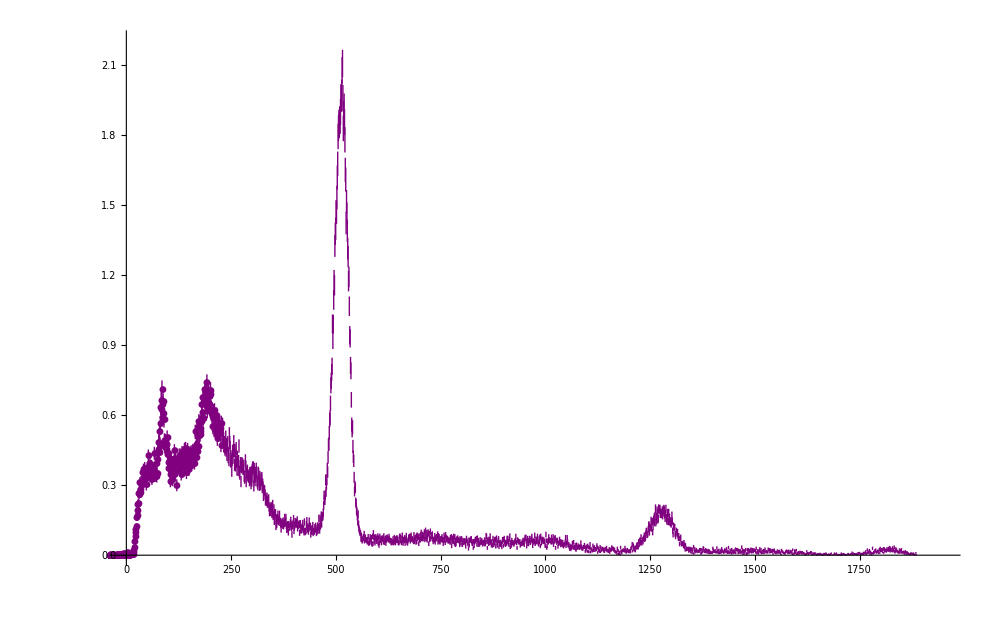

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataNa⟦2;;,{4,7,8,8}⟧,
GridLines->{grids@25,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, keV","N, s^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.001,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)
(*,horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)
}],
Ticks->{myTicX, Automatic}, 
PlotRange->{{0,1950},{0,2.2}}]]
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataCs=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/55/tables/cs.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataCs//TableForm
```

1
 |  |  |  |

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

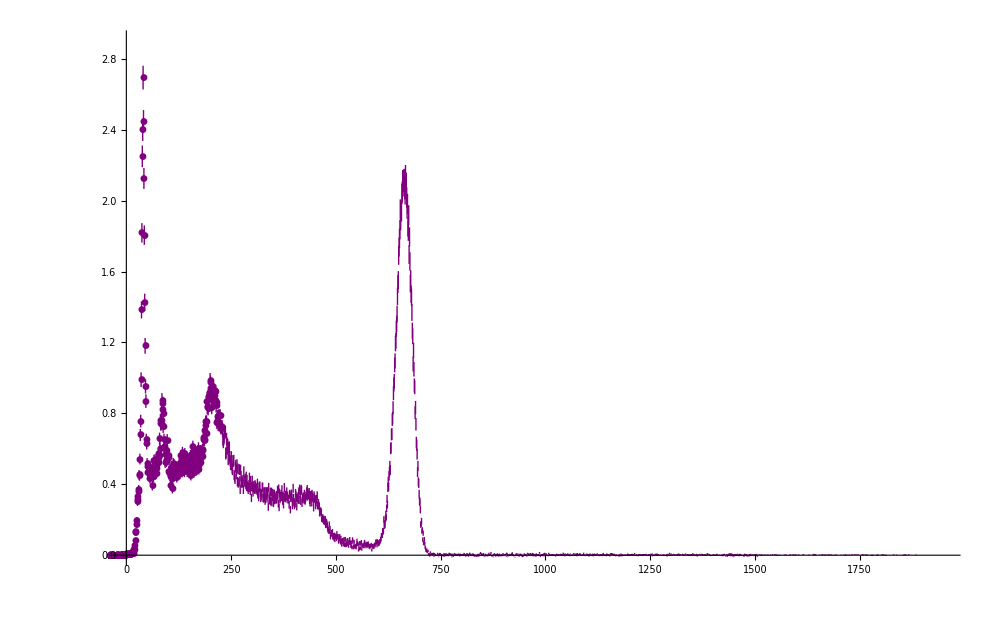

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataCs⟦2;;,{4,7,8,8}⟧,
GridLines->{grids@25,grids@0.1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, keV","N, s^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.001,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)
(*,horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)
}],
Ticks->{myTicX, Automatic}, 
PlotRange->{{0,1950},{0,2.9}}]]
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataCs2=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/55/tables/cs2.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataCs2//TableForm
```

1
 |  |  |  |

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

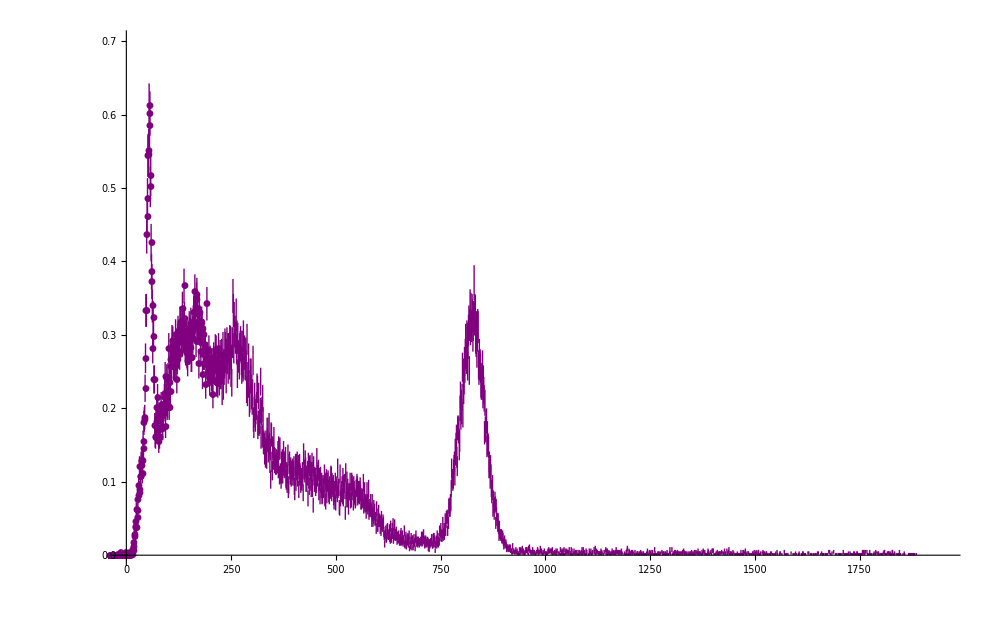

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataCs2⟦2;;,{4,5,8,8}⟧,
GridLines->{grids@25,grids@0.1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, keV","N, s^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.001,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)
(*,horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)
}],
Ticks->{myTicX, Automatic}, 
PlotRange->{{0,1950},{0,0.7}}]]
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataCo=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/55/tables/co.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataCo//TableForm
```

1
 |  |  |  |

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

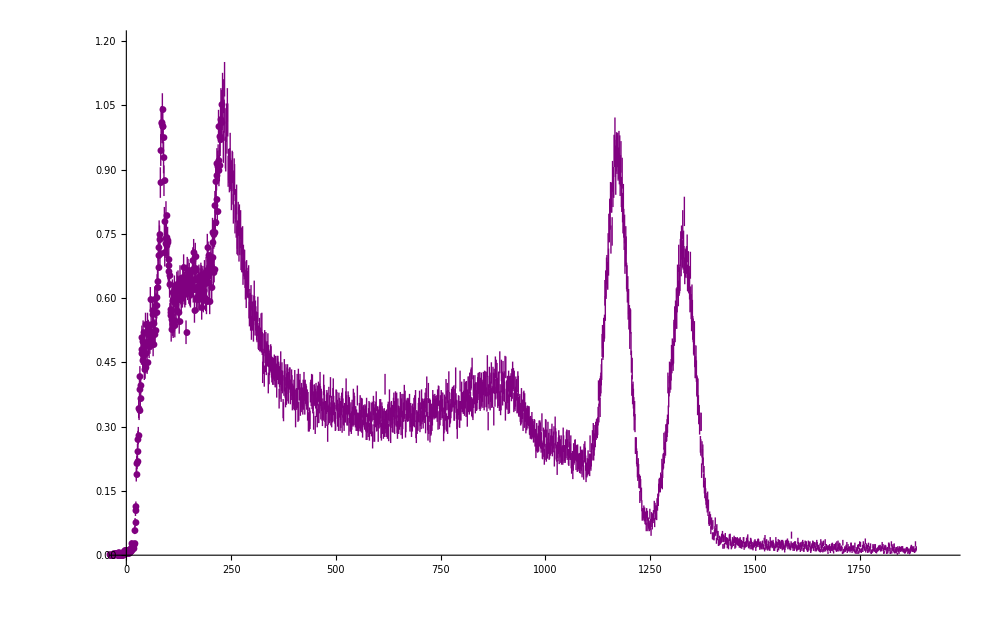

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataCo⟦2;;,{4,5,8,8}⟧,
GridLines->{grids@25,grids@0.1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, keV","N, s^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.001,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)
(*,horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)
}],
Ticks->{myTicX, Automatic}, 
PlotRange->{{0,1950},{0,1.2}}]]
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataAm=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/55/tables/am.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataAm//TableForm
```

1
 |  |  |  |

```mathematica
myTicXAm[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,20}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

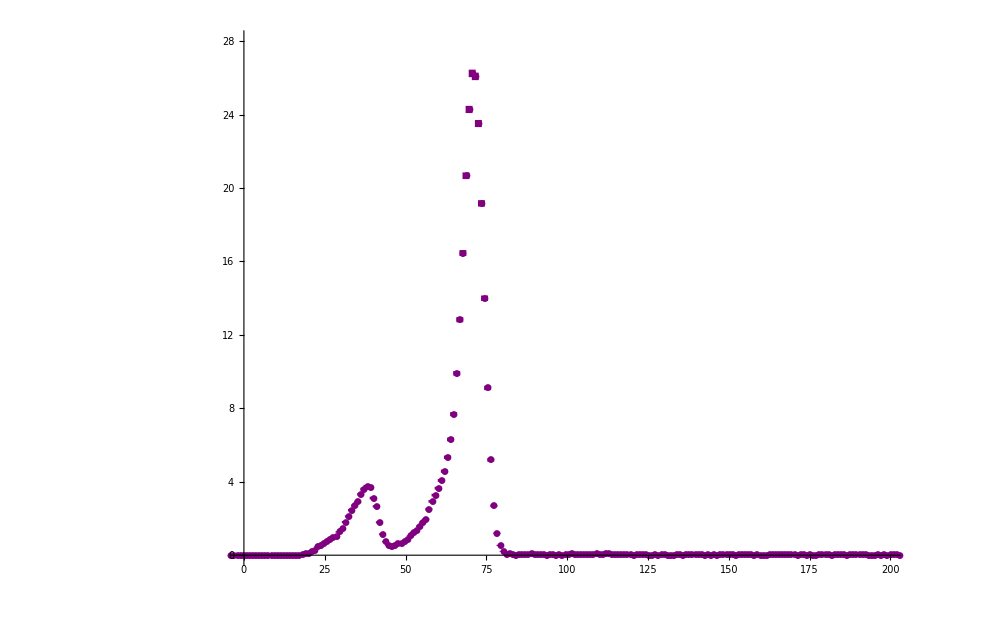

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataAm⟦2;;,{4,7,8,8}⟧,
GridLines->{grids@2.5,grids@1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, keV","N, s^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.005,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)
(*,horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)
}],
Ticks->{myTicXAm, Automatic}, 
PlotRange->{{0,199},{0,28}}]]
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataEu=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/55/tables/eu.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataEu//TableForm
```

1
 |  |  |  |

```mathematica
myTicXAm[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,25}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

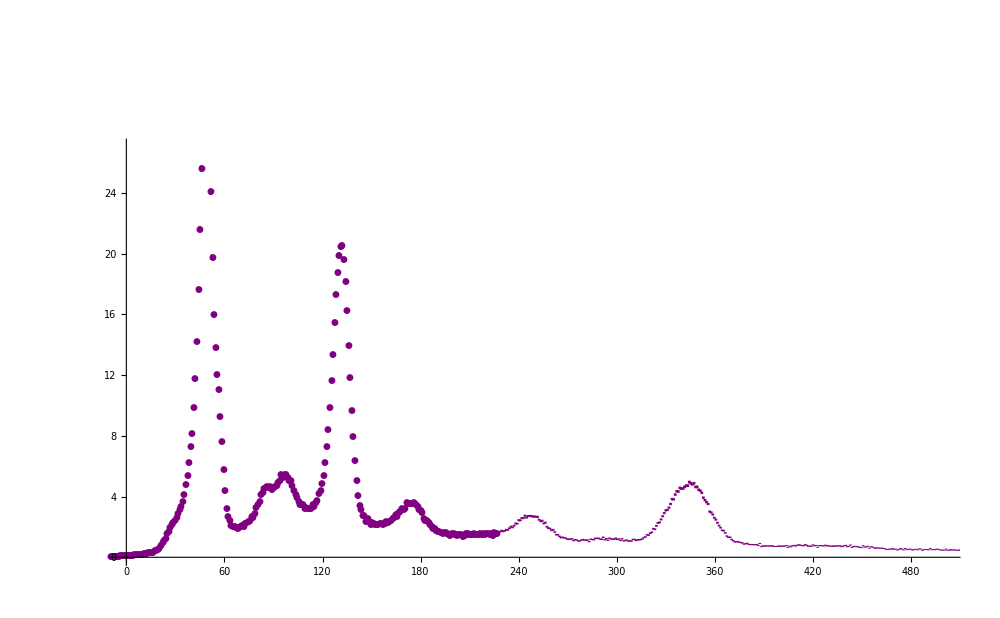

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataEu⟦2;;,{4,7,8,8}⟧,
GridLines->{grids@25,grids@1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, keV","N, s^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.002,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)
(*,horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)
}],
Ticks->{myTicX, Automatic}, 
PlotRange->{{0,500},{0,27}}]]
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataF=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/55/tables/fit.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataF//TableForm
```

N | dN | E
597.48 | 41.98 | 511.
1395.23 | 76.63 | 1275.
754.22 | 47.37 | 662.

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[-60.537+0.957291 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -60.537 | 1.12407 | -53.8554 | 0.0118195
x | 0.957291 | 0.00114874 | 833.339 | 0.000763938

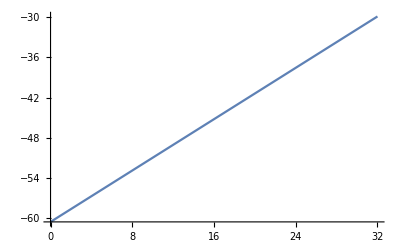

```mathematica
forFit=dataF⟦2;;,{1,3}⟧;
fit=LinearModelFit[forFit,{1,x},x]
fit@"ParameterTable"
Plot[fit["Function"]@x, {x, 0, 32}]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

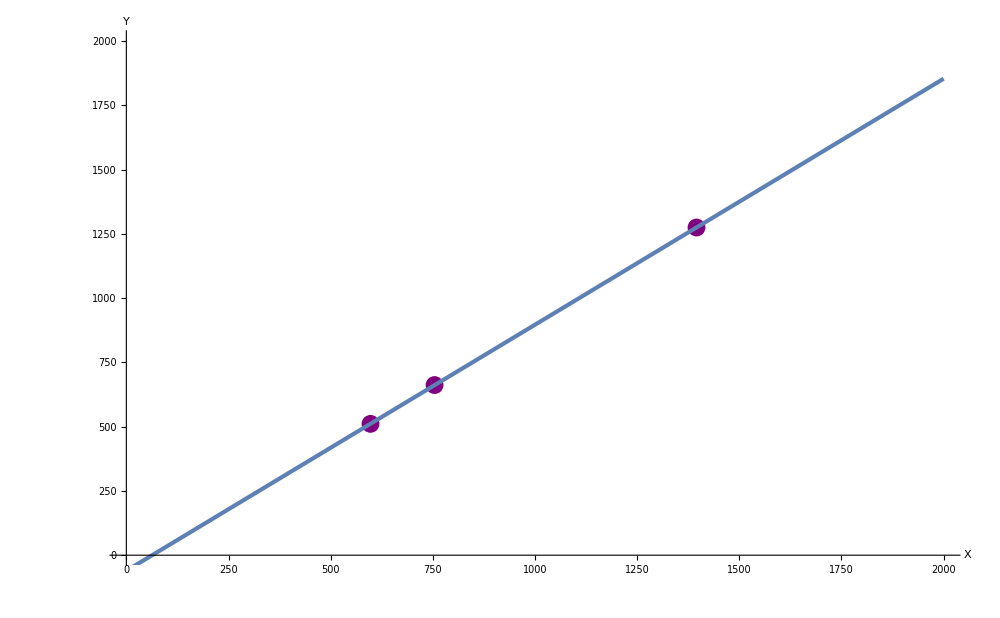

```mathematica
Show[ListPlot[dataF⟦2;;,{1,3}⟧,
GridLines->{grids@2.5,grids@2.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.003 ,Purple},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{0,2000},{0,2000}}], 
Plot[fit["Function"]@x,{x,0,2000}, PlotStyle->Thickness@0.003]]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

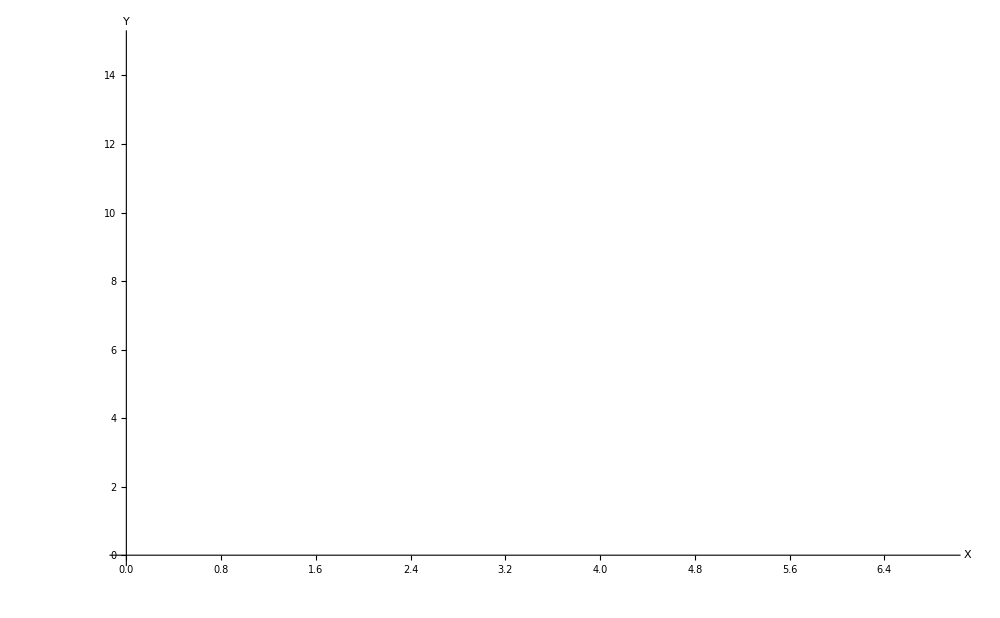

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,4,5,5}⟧,
GridLines->{grids@0.5,grids@0.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{0,6.9},{0,15}}], 
Plot[fit["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,data,{{2;;,All}}];
forTeX//TeXForm
```

## Построение одного графика

### Импорт табличных данных

```mathematica
data=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/55/tables/data_f.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data//TableForm
```

Ni | dNi | Ei | dEi | Ri | R^2 | 1/E | Ec | 
1286.1 | 65.12 | 1170.63 | 62.3388 | 0.0532521 | 2.83579 | 8.54237 | 960.909 | 209.726
1450.59 | 73.3 | 1328.1 | 70.1694 | 0.0528345 | 2.79148 | 7.52955 | 1113.82 | 214.277
597.48 | 41.98 | 511.425 | 40.1871 | 0.0785786 | 5.6 | 19.5532 | 341.045 | 170.381
1395.23 | 76.63 | 1275.1 | 73.3572 | 0.0575304 | 3.30974 | 7.8425 | 1062.25 | 212.85
754.22 | 47.37 | 661.471 | 45.3469 | 0.0685546 | 4.69973 | 15.1178 | 477.162 | 184.309
135.57 | 9.45 | 69.2429 | 9.0464 | 0.130647 | 17.0687 | 144.419 | 14.7642 | 54.4787
199.01 | 12.26 | 129.973 | 11.7364 | 0.0902983 | 9.1 | 76.9388 | 43.8243 | 86.1492
421.72 | 30.43 | 343.172 | 29.1304 | 0.0848857 | 6.55 | 29.1399 | 196.714 | 146.458

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[2.74367+0.097081 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.74367 | 0.40169 | 6.83031 | 0.000483641
x | 0.097081 | 0.00673854 | 14.4068 | 7.00479×10^-6

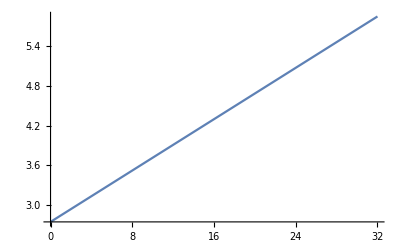

```mathematica
forFitR=data⟦2;;,{7,6}⟧;
fitR=LinearModelFit[forFitR,{1,x},x]
fitR@"ParameterTable"
Plot[fitR["Function"]@x, {x, 0, 32}]
```

```mathematica
{{"", "Estimate", "Standard Error"}, {1, 2.7436692457010494, 0.4016901332986583}, {x, 0.09708096012183612, 0.006738541473920926}}
```

{{,Estimate,Standard Error},{1,2.74367,0.40169},{x,0.097081,0.00673854}}

```mathematica
TeXForm[{{"","Estimate","Standard Error"},{1,2.7436692457010494,0.4016901332986583},{x,0.09708096012183612,0.006738541473920926}}]
```

\left(
\begin{array}{ccc}
 \text{} & \text{Estimate} & \text{Standard Error} \\
 1 & 2.74367 & 0.40169 \\
 x & 0.097081 & 0.00673854 \\
\end{array}
\right)

```mathematica
TeXForm[{{"","Estimate","Standard Error"},{1,2.9043847795655204,0.6127701954860335},{x,0.09383987809554156,0.010279509089149593}}]
```

\left(
\begin{array}{ccc}
 \text{} & \text{Estimate} & \text{Standard Error} \\
 1 & 2.90438 & 0.61277 \\
 x & 0.0938399 & 0.0102795 \\
\end{array}
\right)

```mathematica
(*χ=√(Total[(print@fitR["FitResiduals"]/print@forFit1Cr)^2]/(Length[forFit1]-degOfFree));
χ^2*)
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

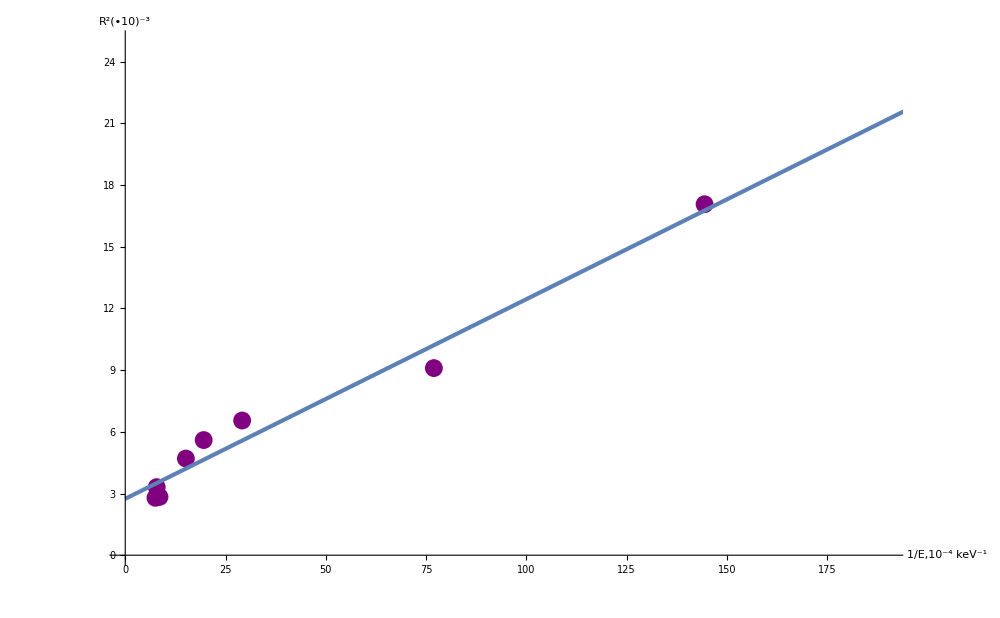

```mathematica
Show[ListPlot[data⟦2;;,{7,6}⟧,
GridLines->{grids@5,grids@2.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"1/E,10^-4 keV^-1","R^2(•10)^-3"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.003 ,Purple},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{0,190},{0,25}}], 
Plot[fitR["Function"]@x,{x,0,300}, PlotStyle->Thickness@0.003]]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,4,5,5}⟧,
GridLines->{grids@0.5,grids@0.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{0,6.9},{0,15}}], 
Plot[fit["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeXd=MapAt[dropLastDot@*ToString,datad,{{2;;,All}}];
forTeXd//TeXForm
```

StringTake::take: Cannot take positions -1 through -1 in "".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

\left(
\begin{array}{ccc}
 \text{} & \unicode{0443} & \text{} \\
 \text{n} & 511.4 & 190 \\
 \text{} & 661.5 & 205 \\
 \text{} & 1328.1 & 230 \\
 \text{} & 129.973 & 95 \\
 \text{} & 343.172 & 170 \\
\end{array}
\right)

### Импорт табличных данных

```mathematica
datad=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/55/tables/com.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
datad//TableForm
```

| у | 
n | 511.4 | 190.
 | 661.5 | 205.
 | 1328.1 | 230.
 | 129.973 | 95.
 | 343.172 | 170.

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFitE=datad⟦2;;,{2,3}⟧
fitE=LinearModelFit[forFitE,{1,x},x]
fitE@"ParameterTable"
Plot[fitE["Function"]@x, {x, 0, 32}]
```

{{511.4,190.},{661.5,205.},{1328.1,230.},{129.973,95.},{343.172,170.}}

```mathematica
TableForm[forFitE]
```

511.4 | 190.
661.5 | 205.
1328.1 | 230.
129.973 | 95.
343.172 | 170.

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

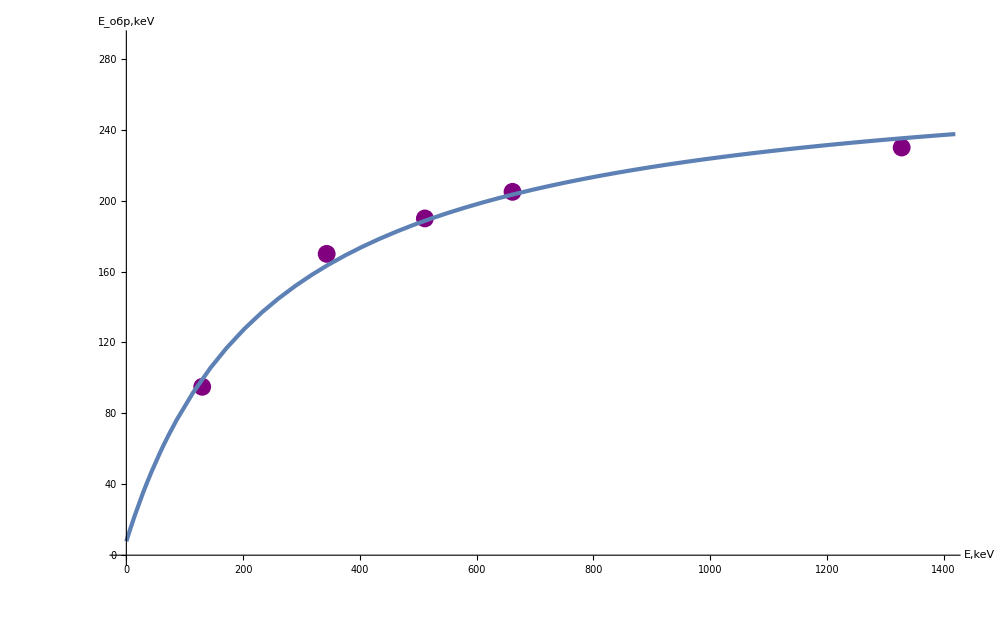

```mathematica
Show[ListPlot[datad⟦2;;,{2,3}⟧,
GridLines->{grids@50,grids@25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E,keV","E_(:043e:0431:0440),keV"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.003 ,Purple},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{0,1400},{0,290}}], 
Plot[fitEe["Function"]@x,{x,0,1420}, PlotStyle->Thickness@0.003]]
```

```mathematica
{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {1, 23.433236177220024, 12.36535158446957, 1.8950723735709474, 0.1985629233249604}, {x, 0.9637555437709995, 0.015838134607259406, 60.85031903499938, 0.00026995936032492285}}
```

{{,Estimate,Standard Error,t-Statistic,P-Value},{1,23.4332,12.3654,1.89507,0.198563},{x,0.963756,0.0158381,60.8503,0.000269959}}

```mathematica
TableForm[%413]
```

```mathematica
{{"", "Estimate", "Standard Error"}, {1, 23.433236177220024, 12.36535158446957}, {x, 0.9637555437709995, 0.015838134607259406}}
```

{{,Estimate,Standard Error},{1,23.4332,12.3654},{x,0.963756,0.0158381}}

```mathematica
TeXForm[{{"","Estimate","Standard Error"},{1,23.433236177220024,12.36535158446957},{x,0.9637555437709995,0.015838134607259406}}]
```

\left(
\begin{array}{ccc}
 \text{} & \text{Estimate} & \text{Standard Error} \\
 1 & 23.4332 & 12.3654 \\
 x & 0.963756 & 0.0158381 \\
\end{array}
\right)

```mathematica
model =a*x/(1+x/255)+c
```

c+(a x)/(1+x/255)

```mathematica
(*fit1=NonlinearModelFit[forFitN⟦All,{1,2}⟧,{model1,-5<g<5},{{a,5},{c,0.3},{d,2},{f, 4.4},{e,2},{g,0}},x]*)
fitEe=NonlinearModelFit[forFitE,model,{a,c},x]
(*fitP=NonlinearModelFit[forFitN⟦All,{3,2}⟧,{modelm(*,-0.2<g<1,1<a<4.5,3<b<4.1,0<c<10, 0.19<d<5, 4<f<5,0<e<10, -5<g<5*)},{{a,4.5},{b,1000},{c,100},{d,3},{f, 4.4},{e,2},{g,-0.2}},x(*, MaxIterations->10000*)]*)
fitEe@"ParameterTable"
(*fitP@"ParameterTable"*)
(*Plot[fit["Function"]@x, {x, 0, 32}] *)
```

FittedModel[7.85222+(1.06274 x)/(1+x/255)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.06274 | 0.0584254 | 18.1896 | 0.000362489
c | 7.85222 | 9.68542 | 0.810725 | 0.476869

```mathematica
{{"", "Estimate", "Standard Error"}, {a, 1.0627361013750076, 0.05842540954537407}, {c, 7.852219047928952, 9.685423207030027}}
```

{{,Estimate,Standard Error},{a,1.06274,0.0584254},{c,7.85222,9.68542}}

```mathematica
TeXForm[{{"","Estimate","Standard Error"},{a,1.0627361013750076,0.05842540954537407},{c,7.852219047928952,9.685423207030027}}]
```

\left(
\begin{array}{ccc}
 \text{} & \text{Estimate} & \text{Standard Error} \\
 a & 1.06274 & 0.0584254 \\
 c & 7.85222 & 9.68542 \\
\end{array}
\right)

```mathematica
Solve[3 x^2-2x*(1000+1331+1728)+1000*1331+1331*1728+1728*1000==0,x]
```

{{x→1/3 (4059-√398577)},{x→1/3 (4059+√398577)}}

```mathematica
N[{{x->1/3 (4059-√398577)},{x->1/3 (4059+√398577)}}]
```

{{x→1142.56},{x→1563.44}}

```mathematica
x=1142
```

1142

```mathematica
(x-1000)(x-1331)(x-1728)
```

15727068

```mathematica
c=1
Exp[c]+1/c
```